## Notebook Basics

Input cells contain commands. Text, Section, etc.  cells contain words etc. In addition to computing things Mathematica also typesets equations etc.

⇧⌤ executes commands in an Input cell.

Square braces (on the far side) let you select a cell or group of cells

## Mathematica Basics

Commands are case sensitive.  Function arguments are enclosed by “[ ]”. Output is suppressed with “;”

⇧⌤ executes commands

Commands usually tell you exactly what they do. For suitable matrices A and vectors b

“MatrixPlot[A]” and “ListPlot[b]” draw standard pictures.

“x=LinearSolve[A, b]”  computes a vector x satisfying A x=b.

“{λ,V}=Eigensystem[A]”  gives lists of eigenvalues λ_1,λ_2… and eigenvectors v_1,v_2,… satisfying A v_i=λ_i v_i.

We are going to learn what (and a tiny bit of how) these commands do.

### Eigenstuff

The following cell imports a matrix “A” from a NIST repository, plots the matrix, computes eigenstuff and of the matrix and plots the eigenvalues on a log scale.  The origin of the matrix is described at https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc2/bcsstk14.html

SparseArray[…]

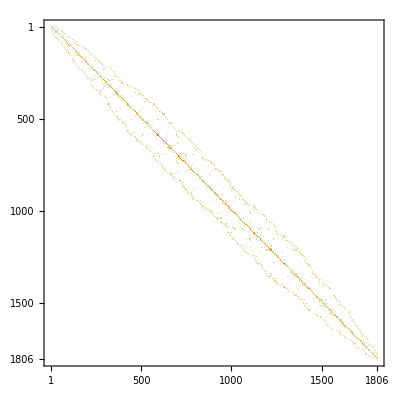

Eigensystem::arh: Because finding 1806 out of the 1806 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

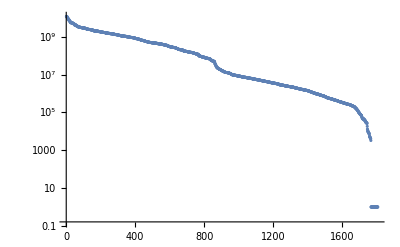

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc2/bcsstk14.mtx.gz"]
MatrixPlot[A]
{λ,V}=Eigensystem[A];
ListLogPlot[λ,PlotRange->All,GridLines->Automatic]
```

### LinearSolve

The following cell imports a matrix “A” from a NIST repository, plots the matrix and demonstrates LinearSolve.  The origin of the matrix is described at
https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc3/bcsstk24.html

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc3/bcsstk24.mtx.gz"];
MatrixPlot[A];
{m,n}=Dimensions[A];
xIn=Cos[Range[0.0,π,π/(n-1)]];
b=A.xIn;
xOut=LinearSolve[A,b];
TabView[{"x_in"->ListPlot[xIn],"b"->ListPlot[b],"x_Out"->ListPlot[xOut],
"x_in-x_Out"->ListPlot[xIn-xOut,PlotRange->All]}]
```

1234

### Matrix and Vector Arithmetic

{{4,4},{4,3},{3,3},{3,3},{3}}

{(0.644157 | 0.853615 | 0.153554 | -0.671473
-0.30793 | -0.0370674 | 0.408019 | -0.808894
0.656976 | -0.225173 | -0.129362 | 0.0534525
-0.398968 | -0.587753 | 0.472302 | -0.633929),(-0.179322 | 0.721997 | 0.544257
0.48024 | 0.124428 | 0.676229
0.317316 | -0.908238 | 0.681294
-0.209858 | 0.0130862 | 0.779089),(-0.310964 | 0.0972055 | 0.558339
-0.419969 | 0.00232818 | 0.354382
-0.551777 | -0.20145 | -0.145241),(0.717559 | 0.277036 | 0.164456
0.624531 | 0.99886 | 0.236613
0.242398 | 0.452913 | -0.35631)}

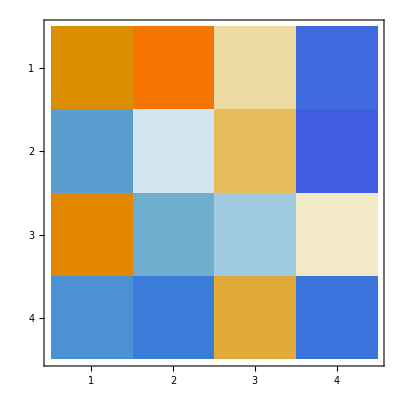
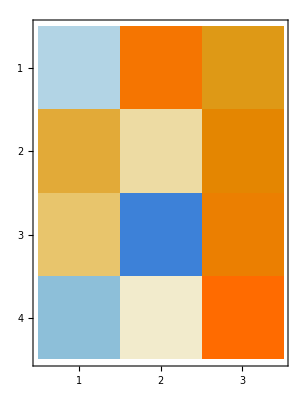
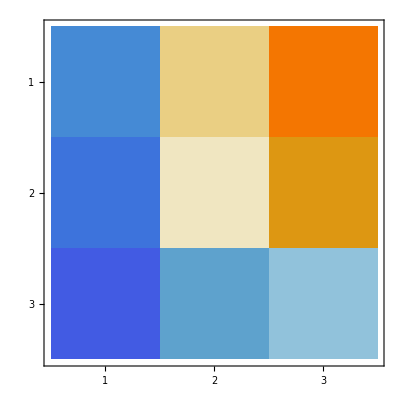
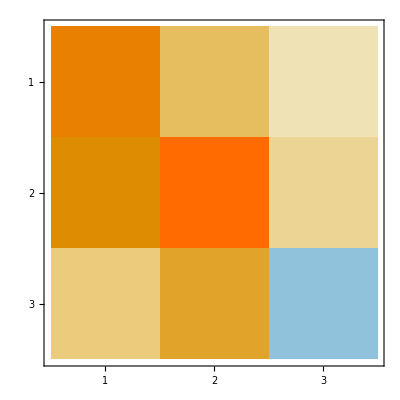

```mathematica
{m,n}={4,3};
A1=RandomReal[{-1,1},{m,m}];
A2=RandomReal[{-1,1},{m,n}];
A3=RandomReal[{-1,1},{n,n}];
A4=RandomReal[{-1,1},{n,n}];
x=RandomReal[{-1,1},n];
Map[Dimensions,{A1,A2,A3,A4,x}]
Map[MatrixForm,{A1,A2,A3,A4}]
Map[MatrixPlot,{A1,A2,A3,A4}]
```